## Stan data analysis

### Full- and Half-Sibling models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/stephan_schiffels/dev/celtic_relationship_analysis

```mathematica
readStanDataset[filename_]:=Module[{rawD},
rawD=Import["model_siblings_output.csv"]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&];
Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
]
```

```mathematica
ds=readStanDataset["model_siblings_output.csv"]
```

Dataset[<>]

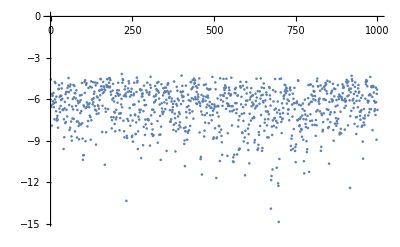

```mathematica
ListPlot[ds[[All,"lp__"]]]
```

Trajectory looks fine, no obvious burn-in or something.

```mathematica
ds[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
variableNames={"birth_date_mother","mother_age_hochdorf","mother_age_asperg","age_hochdorf","age_asperg","burial_date_hochdorf","burial_date_asperg"};
```

```mathematica
priorDistributions=AssociationThread[
variableNames,
{
UniformDistribution[{-600,-500}],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
NormalDistribution[-530,6],
NormalDistribution[-490,6]
}
]
```

<|birth_date_mother→UniformDistribution[{-600,-500}],mother_age_hochdorf→NormalDistribution[30,6],mother_age_asperg→NormalDistribution[30,6],age_hochdorf→NormalDistribution[45,6],age_asperg→NormalDistribution[30,6],burial_date_hochdorf→NormalDistribution[-530,6],burial_date_asperg→NormalDistribution[-490,6]|>

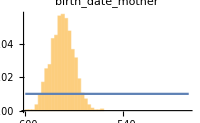
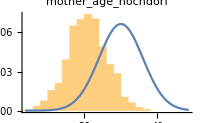
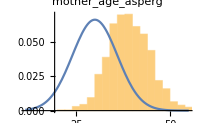
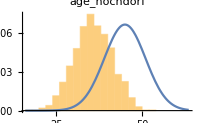
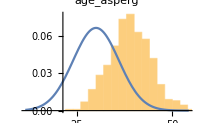
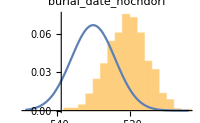
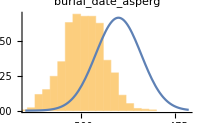

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
d=ds[All,v];
pd=priorDistributions[[v]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{v,variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[ds[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
birth_date_mother | -588.656 | -577.266 | -566.133
mother_age_hochdorf | 11.2697 | 20.7575 | 29.6282
mother_age_asperg | 30.7118 | 38.774 | 48.4151
age_hochdorf | 26.6839 | 35.6367 | 44.8355
age_asperg | 29.9564 | 38.981 | 47.6571
burial_date_hochdorf | -529.527 | -520.727 | -512.087
burial_date_asperg | -508.492 | -499.129 | -490.57

### Computing Marginal Likelihood

#### Naive prior sampling method

```mathematica
combinedPrior=ProductDistribution@@(Values[priorDistributions][[;;5]])
```

ProductDistribution[UniformDistribution[{-600,-500}],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[45,6],NormalDistribution[30,6]]

```mathematica
logLSiblings[paramVector_]:=Module[{mothersBirthDate,birthAgeH,birthAgeA,ageH,ageA,burialDateH,burialDateA},
{mothersBirthDate,birthAgeH,birthAgeA,ageH,ageA}=paramVector;
burialDateH=mothersBirthDate+birthAgeH+ageH;
burialDateA=mothersBirthDate+birthAgeA+ageA;
LogLikelihood[NormalDistribution[-530.,6],{burialDateH}]+
LogLikelihood[NormalDistribution[-490.,6],{burialDateA}]
]
```

```mathematica
priorSamples=RandomVariate[combinedPrior,100000];
```

```mathematica
loglValues=logLSiblings/@priorSamples;
```

```mathematica
Ordering[{5,2,4,7,1},-1]
```

{4}

```mathematica
Max[loglValues]
```

-6.1728

```mathematica
maxIndex=Ordering[loglValues,-1]//First
```

93158

```mathematica
priorSamples[[maxIndex]]
```

{-572.091,17.5786,39.4608,29.159,36.9284}

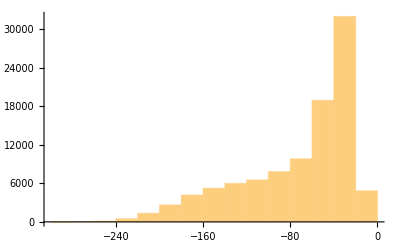

```mathematica
Histogram[loglValues]
```

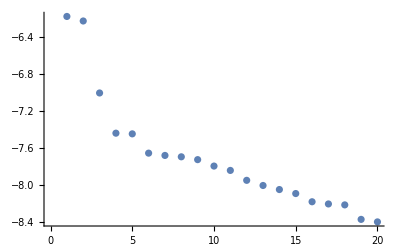

```mathematica
ListPlot[ReverseSort[loglValues][[;;20]]]
```

```mathematica
scalingFactor=Max[loglValues]
```

-6.1728

```mathematica
avgL=Log[Mean[Exp[loglValues-scalingFactor]]]+scalingFactor
```

-15.3195

```mathematica
avgL=Table[
Log[Mean[Exp[p-scalingFactor]]]+scalingFactor,
{p,Partition[loglValues,10000]}
]
```

{-15.2261,-14.8836,-14.9848,-15.5901,-15.982,-16.221,-15.6431,-15.3151,-15.4073,-14.8308}

#### Method by Reichl et al.

```mathematica
posteriorDraws=Normal[ds[All,Values]][[All,8;;12]];
```

```mathematica
posteriorLogLvalues=logLSiblings/@posteriorDraws;
```

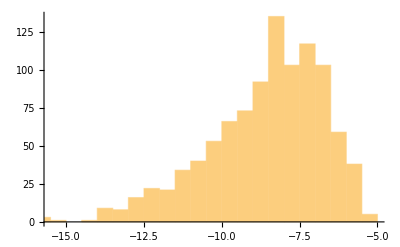

```mathematica
Histogram[posteriorLogLvalues]
```

```mathematica
ρ=Median[posteriorLogLvalues]
θStar=Max[posteriorLogLvalues]
d=Covariance[posteriorDraws]
```

-8.26928

-5.44593

{{47.9274,-14.0027,-16.7341,-17.4517,-14.6524},{-14.0027,28.5466,6.94773,-7.16135,2.79157},{-16.7341,6.94773,29.635,5.75356,-7.3986},{-17.4517,-7.16135,5.75356,29.8205,6.43217},{-14.6524,2.79157,-7.3986,6.43217,28.9924}}

```mathematica
pointInVolumeA1Q[params_,ρ_]:=logLSiblings[params]>ρ
```

```mathematica
pointInVolumeQ2Q[params_,θStar_,mat_]:=Module[{v,i},
v=params-θStar;
i=Inverse[mat];
v.Inverse[mat].v<1
]
```

```mathematica
pointInVolumeAQ[params_,θStar_,mat_,ρ_]:=pointInVolumeA1Q[params,ρ]&&pointInVolumeQ2Q[params,θStar,mat]
```

```mathematica
posteriorDraws//Length
```

1000

```mathematica
Length[Select[posteriorDraws,pointInVolumeAQ[#,θStar,d 14368.5,ρ]&]]
```

490

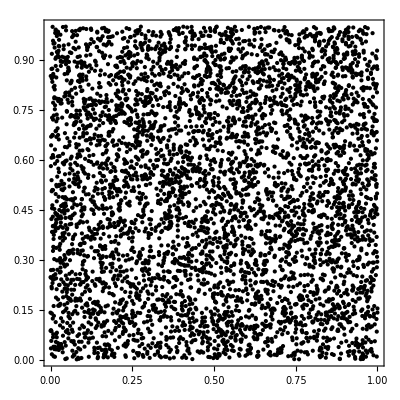

```mathematica
randomPoints=RandomVariate[UniformDistribution[10000]]//Partition[#,2]&;
colors=Table[If[pointInVolumeQ2Q[p,{0.5,0.5},DiagonalMatrix[{0.2,.4}^2]],Red,Blue],{p,randomPoints}];
Graphics[Point[randomPoints,VertexColors->colors],AspectRatio->1,ImagePadding->20,Frame->True]
```

```mathematica
(*This is from Reichl et al 2020*)
getEllDraw[θStar_,mat_]:=Module[{k,rs,pt,λs,λh,eVals,eVecs},
k=Length@mat;
rs=RandomVariate[UniformDistribution[]];
pt=RandomVariate[NormalDistribution[],k];
λs=Total[pt^2];
λh=rs^(1/k)/√λs;
eVals=Eigenvalues[mat];
eVecs=Transpose@Eigenvectors[mat];
(λh pt eVals).eVecs+θStar
]
```

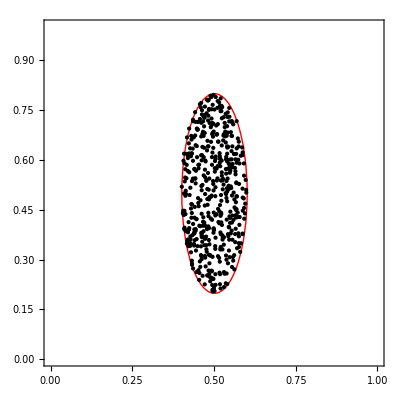
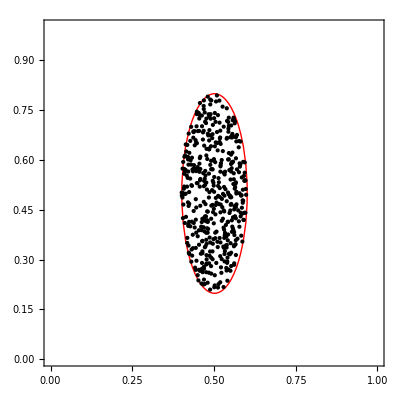

```mathematica
sqrtRadii={.1,.3};
ellipsoidPoints=Table[getEllDraw[{0.5,0.5},DiagonalMatrix[sqrtRadii]],500];
opts={Frame->True,AspectRatio->1,ImagePadding->20,ImageSize->400};
Row[{
Graphics[
{
Red,Circle[{0.5,0.5},sqrtRadii],
Black,
Opacity[1],
Point[ellipsoidPoints]
},PlotRange->{{0,1},{0,1}},Sequence@@opts],
Graphics[
{
Red,Circle[{0.5,0.5},sqrtRadii],
Black,
Opacity[1],
Point[Select[randomPoints,pointInVolumeQ2Q[#,{0.5,0.5},DiagonalMatrix[sqrtRadii^2]]&]]
},PlotRange->{{0,1},{0,1}},Sequence@@opts]
}]
```

```mathematica
(*This is from Reichl et al. 2020*)
getEllipsoidVolume[mat_]:=Module[{k=Length@mat,v,e,i},
v=Table[0,k+1];
e=Eigenvalues@mat;
v[[1]]=Log[1];
v[[2]]=Log[2];
For[i=3,i<=k+1,i++,v[[i]]=Log[(2Pi)/(i-1)]+v[[i-2]]];
v[[k+1]]+Total[Log@Sqrt[e]]
]
```

```mathematica
getEllipsoidVolume[DiagonalMatrix[{0.5,2}]]//Exp
```

3.14159